## Depict Tiles

```mathematica
TileVertices[step_][or_,dir_,ref_,pt_] := With[{
basicVertices = AnglePath[{
		{step[[2]], -Pi/6+dir*Pi/6},
		{step[[2]], Pi/3},
		{step[[1]], Pi/2},
		{step[[1]], Pi/3},
		{step[[2]], -Pi/2},
		{step[[2]], Pi/3},
		{step[[1]], Pi/2},
		{step[[1]], -Pi/3},
		{step[[2]], Pi/2},
		{step[[2]], -Pi/3},
		{step[[1]], Pi/2},
		{step[[1]], Pi/3},
		{step[[1]], 0}
	}]
},
	Expand[# + or&/@(If[ref,{-#[[1]],#[[2]]},#]&/@((#-basicVertices[[pt]])&/@basicVertices))]
]
```

```mathematica
TileEdges[step_][or_,dir_,ref_,pt_] := Partition[TileVertices[step][or,dir,ref,pt], 2, 1, 1]
```

```mathematica
Tile[step_][or_,dir_,ref_,pt_] := Polygon[TileVertices[step][or,dir,ref,pt]]
```

```mathematica
hatVertices:=TileVertices[{1, Sqrt[3]}];
hatEdges:=TileEdges[{1, Sqrt[3]}];
hat:=Tile[{1, Sqrt[3]}];
```

```mathematica
spectreVertices:=TileVertices[{1,1}];
spectreEdges:=TileEdges[{1,1}];
spectre:=Tile[{1,1}];
```

```mathematica
canonicalHat[or_,dir_,ref_,pt_]:={hatVertices[or,dir,ref,pt][[1]], dir, ref, 1}
```

## Manipulate Cluster

```mathematica
rotateCluster[code_,r_]:=Replace[code,
{
{pos_,dir_,False,pt_}:>{Expand[RotationMatrix[r*Pi/6].pos],Mod[dir+r,12],False,pt},
{pos_,dir_,True,pt_}:>{Expand[RotationMatrix[r*Pi/6].pos],Mod[dir-r,12],True,pt}
},
{1}
];

translateCluster[code_,vec_]:={#1+vec,#2,#3,#4}&@@@code;

placeCluster[pos_,dir_,code_]:=translateCluster[rotateCluster[code,dir],pos];
```

```mathematica
rotateTiling[tiling_, r_] := <|
	"code" -> rotateCluster[tiling["code"], r],
	"controlPoints" -> (Expand[RotationMatrix[r * Pi/6] . #] & /@ tiling["controlPoints"])
|>

translateTiling[tiling_, vec_] := <|
	"code" -> translateCluster[tiling["code"], vec],
	"controlPoints" -> (Expand[# + vec] & /@ tiling["controlPoints"])
|>

placeTiling[pos_, dir_, tiling_] := translateTiling[rotateTiling[tiling, dir], pos];
```

```mathematica
reflectCode[code_]:=Apply[{{-#1,#2}&@@#1,#2,#3/.{True->False,False->True},#4}&,code,{1}];
reflectTiling[tiling_] := <|"code"->reflectCode[tiling["code"]],"controlPoints"->Apply[{-#1,#2}&,tiling["controlPoints"],1]|>
```

## Substitution Rule

### spectre rule works for Tile(1,1), (Tile(1,√3)Tile(√3,1)) pair

```mathematica
substitute["spectre"][tiling1_,tiling2_]:=With[
{
t1=reflectTiling[placeTiling[-tiling1["controlPoints"][[1]],0,tiling1]],
t2=reflectTiling[placeTiling[-tiling2["controlPoints"][[1]],0,tiling2]]
},
Module[
{
T1,T2,T3,T4,T5,T6,T7,T8,
orgionPoint
},
T1=t2;
T2=placeTiling[
Expand[T1["controlPoints"][[4]]-Dot[RotationMatrix[-2Pi/6],(t2["controlPoints"][[2]]-t2["controlPoints"][[1]])]],
-2,t2];

T3=placeTiling[
T2["controlPoints"][[3]],
-2,t2];

T4=placeTiling[
Expand[T3["controlPoints"][[4]]-Dot[RotationMatrix[-4Pi/6],(t2["controlPoints"][[2]]-t2["controlPoints"][[1]])]],
-4,t2];

T5=placeTiling[
Expand[T4["controlPoints"][[4]]-Dot[RotationMatrix[-6Pi/6],(t2["controlPoints"][[2]]-t2["controlPoints"][[1]])]],
-6,t2];

T6=placeTiling[
T5["controlPoints"][[3]],
-6,t2];

T7=placeTiling[
Expand[T6["controlPoints"][[4]]-
Dot[RotationMatrix[-8Pi/6],(t2["controlPoints"][[2]]-t2["controlPoints"][[1]])]],
-8,t2];

T8=placeTiling[
Expand[T7["controlPoints"][[4]]-Dot[RotationMatrix[-4Pi/6],(t1["controlPoints"][[4]]-t1["controlPoints"][[1]])]],
-4,t1
];

With[{newOriginPt=T7["controlPoints"][[3]]},
<|
"tiling1"-><|
"code"->translateCluster[Join@@(#["code"]&/@{T1,T2,T4,T5,T6,T7,T8}),-newOriginPt],
"controlPoints"->
(#-newOriginPt&/@{T7["controlPoints"][[3]],T6["controlPoints"][[2]],T4["controlPoints"][[3]],T1["controlPoints"][[2]]})
|>,
<|
"tiling2"-><|
"code"->translateCluster[Join@@(#["code"]&/@{T1,T2,T3,T4,T5,T6,T7,T8}),-newOriginPt],
"controlPoints"->
(#-newOriginPt&/@{T7["controlPoints"][[3]],T6["controlPoints"][[2]],T4["controlPoints"][[3]],T1["controlPoints"][[2]]})
|>
|>
|>
]
]
]
```

## Visualization

```mathematica
Options[depictControlPoints]=Join[
Options[Graphics],
{
step->{1,1},
ChooseColor->{LightBlue,Yellow},
EdgeForm->Black,
ShowControlPoints->True
}
];
depictControlPoints[tile_,opt:OptionsPattern[]]:=Graphics[
{
	tile["code"]/.{
			{pos_,or_,False,v_}:>
				{
Opacity[.6],EdgeForm[OptionValue[EdgeForm]],OptionValue[ChooseColor][[1]],
Tile[OptionValue[step]][pos,or,False,v]
},
			{pos_,or_,True,v_}:>
				{
Opacity[.6],EdgeForm[OptionValue[EdgeForm]],OptionValue[ChooseColor][[2]],
Tile[OptionValue[step]][pos,or,True,v]
}
	}
	,
If[
OptionValue[ShowControlPoints],
{
Red,PointSize[.03],
Point[tile["controlPoints"]],
Line[Partition[tile["controlPoints"],2,1,1]]
},
Nothing
]
}
,
Sequence@@FilterRules[{opt},Options[Graphics]]
];
```

## Tiles Information

```mathematica
s1Tile=<|
"code"->{{{0,0},4,True,1}},
"controlPoints"->spectreVertices[{0,0},4,True,1][[{6,4,2,12}]]
|>;
s2Tile=<|
"code"->{{{0,0},4,True,1},{spectreVertices[{0,0},4,True,1][[1]],3,True,9}},
"controlPoints"->spectreVertices[{0,0},4,True,1][[{6,4,2,12}]]
|>;
```

## Main

```mathematica
res=NestList[Values[substitute["spectre"][#[[1]],#[[2]]]]&,{s2Tile,s1Tile},3];
```

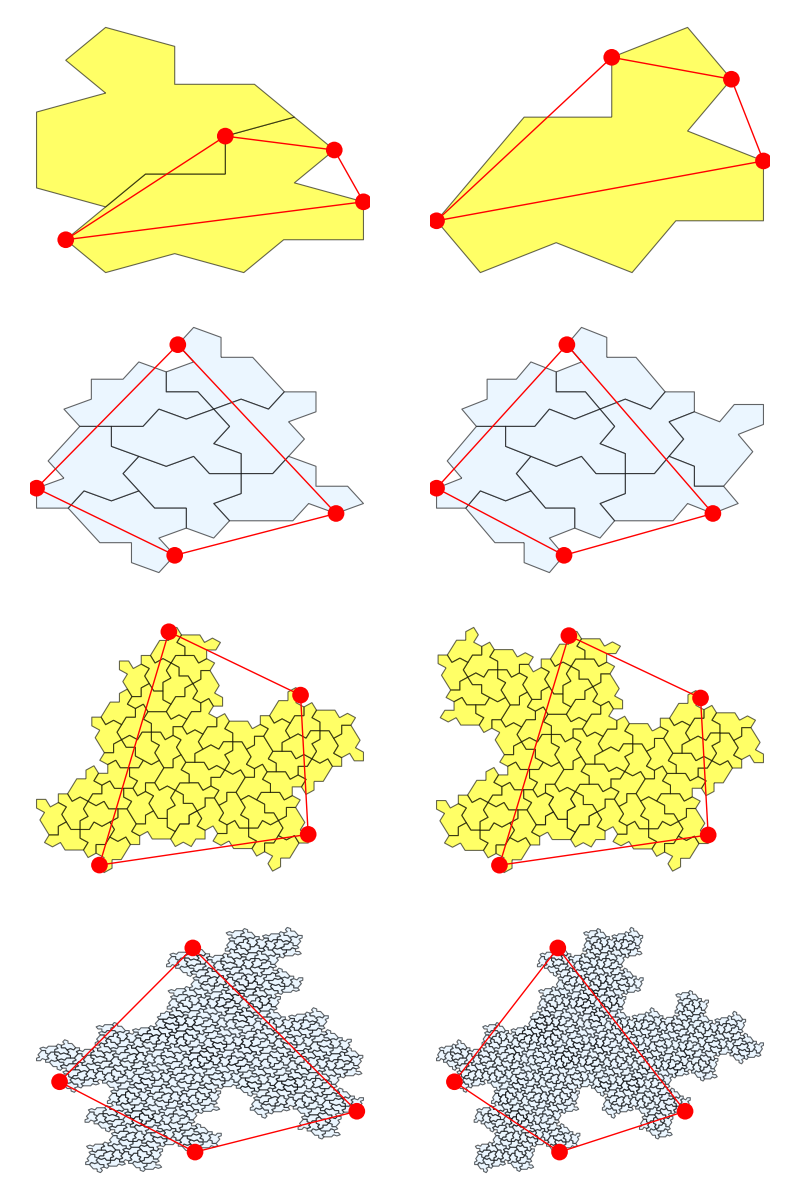

```mathematica
Map[depictControlPoints,res,{2}]//Grid
```